```mathematica
ClearAll["Global`*"]
AppendTo[$Path,NotebookDirectory[]]
```

{/home/frank/.Mathematica/DocumentationIndices,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Links,/home/frank/.Mathematica/Kernel,/home/frank/.Mathematica/Autoload,/home/frank/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/frank,/usr/local/Wolfram/Mathematica/12.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/12.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/12.0/Documentation/English/System,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Data/ICC,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/}

```mathematica
br = Import["snow2prisTr2Export_br.csv"];
br1 = Import["snow2prisTr2Export_br1.csv"];
```

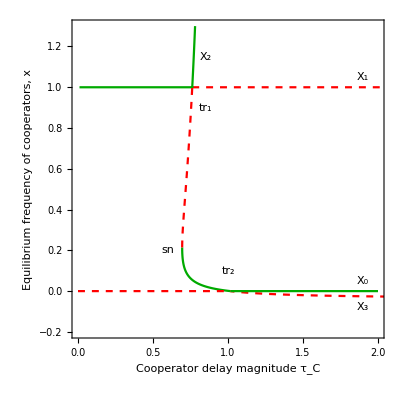

```mathematica
brEig=br[[;;,5]];
brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];
brEqS = ListLinePlot[Transpose[{brtauS ,brXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];
brEqR = ListLinePlot[Transpose[{brtauR ,brXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];

br1Eig=br1[[;;,5]];

br1IdS = Flatten[Position[br1Eig,_?(#<0&)]];
br1IdR = Flatten[Position[br1Eig,_?(#>0&)]];

br1tauS = br1[[br1IdS ,1]];
br1XS = br1[[br1IdS ,2]];
br1tauR = br1[[br1IdR ,1]];
br1XR = br1[[br1IdR ,2]];

br1XRlow =br1XR[[Flatten[Position[br1XR ,_?(#<0&)]]]];
br1tauRlow =br1tauR [[Flatten[Position[br1XR ,_?(#<0&)]]]];

br1XRmid =br1XR[[Flatten[Position[br1XR ,_?(#>0.2143&)]]]];
br1tauRmid =br1tauR [[Flatten[Position[br1XR ,_?(#>0.2143&)]]]];
br1EqRmid = ListLinePlot[Transpose[{br1tauRmid,br1XRmid}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];

br1XSUp =br1XS[[Flatten[Position[br1XS ,_?(#>1&)]]]];
br1tauSUp =br1tauS[[Flatten[Position[br1XS ,_?(#>1&)]]]];
br1EqUp = ListLinePlot[Transpose[{br1tauSUp,br1XSUp}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.3}}];

br1XSLow =br1XS[[Flatten[Position[br1XS ,_?(#<0.2143&)]]]];
br1tauSLow =br1tauS[[Flatten[Position[br1XS ,_?(#<0.2143&)]]]];
br1EqLow = ListLinePlot[Transpose[{br1tauSLow,br1XSLow}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];


br1EqRlow = ListLinePlot[Transpose[{br1tauRlow ,br1XRlow}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];

zeroEqR =Plot[0.0,{x,0,1.01539969},PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];
zeroEqS =Plot[0.0,{x,1.01539969,2},PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];


lamBr1Low = ListLinePlot[Transpose[{br1[[;;,1]] ,br1[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black,Dashing[{0.04,0.025}]}];


X0L = Graphics[{Text[Style[HoldForm[Subscript[X,0]], Medium,Black], {1.9, 0.05} ]}, Background->White];
X1L = Graphics[{Text[Style[HoldForm[Subscript[X,1]], Medium,Black], {1.9, 1.05} ]}, Background->White];
X2L = Graphics[{Text[Style[HoldForm[Subscript[X,2]], Medium,Black], {0.85, 1.15} ]}, Background->White];
X3L = Graphics[{Text[Style[HoldForm[Subscript[X,3]], Medium,Black], {1.9, -0.08} ]}, Background->White];
snL = Graphics[{Text[Style["sn", Medium,Black], {0.6, 0.2} ]}, Background->White];
tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]], Medium,Black], {0.85, 0.9} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]], Medium,Black], {1, 0.1} ]}, Background->White];
cL = Graphics[{Text[Style["c)",  FontSize->14,Black],  ImageScaled[{.18,.93}] ]}, Background->White];
fullPlotTranscrit =Show[{brEqS,brEqR ,br1EqUp,br1EqLow,br1EqRlow,br1EqRmid,zeroEqR ,zeroEqS,snL,tr1L,tr2L,cL,X0L,X1L,X2L,X3L},PlotRange->{{0.0, 2.0}, {-0.2, 1.3}},Frame->True,
FrameLabel->{"Cooperator delay magnitude τ_C", "Equilibrium frequency\n of cooperators, x"},
Axes->False,LabelStyle->Directive[Black,14],
AspectRatio->1,
PlotRangePadding->None]
```

```mathematica
br = Import["snow2prisPf1Export_br.csv"];
br1 = Import["snow2prisPf1Export_br1.csv"];
```

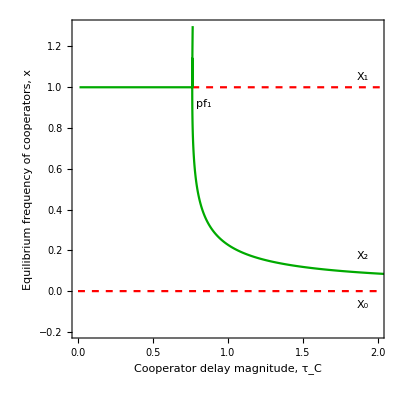

```mathematica
brEig=br[[;;,5]];
brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];
br1Eig=br1[[;;,5]];
br1IdS = Flatten[Position[br1Eig,_?(#<0&)]];
br1tauS = br1[[br1IdS ,1]];
br1XS = br1[[br1IdS ,2]];
br1XSv1 =br1XS [[;;146]];
br1tauSv1 =br1tauS [[;;146]];
br1IdR = Flatten[Position[br1Eig,_?(#>0&)]];
br1tauR = br1[[br1IdR ,1]];
br1XR = br1[[br1IdR ,2]];
brEqS = ListLinePlot[Transpose[{brtauS ,brXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.3}}];
brEqR = ListLinePlot[Transpose[{brtauR ,brXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.3}}];
br1EqS = ListLinePlot[Transpose[{br1tauS ,br1XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.3}}];
br1EqRv = ListLinePlot[Transpose[{br1tauR ,br1XR}],PlotStyle->{Red, Dashed}];
zeroEqR =Plot[0.0,{x,0,2.0},PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.3}}];
pfL = Graphics[{Text[Style[HoldForm[Subscript[pf,1]], Medium,Black], {0.84, 0.92} ]}, Background->White];
bL = Graphics[{Text[Style["b)",  FontSize->14,Black], ImageScaled[{.18,.93}] ]}, Background->White];
X0L = Graphics[{Text[Style[HoldForm[Subscript[X,0]], Medium,Black], {1.9, -0.07} ]}, Background->White];
X1L = Graphics[{Text[Style[HoldForm[Subscript[X,1]], Medium,Black], {1.9, 1.05} ]}, Background->White];
X2L = Graphics[{Text[Style[HoldForm[Subscript[X,2]], Medium,Black], {1.9, 0.17} ]}, Background->White];
fullPlotPitch =Show[{brEqS,brEqR,br1EqS,br1EqRv ,zeroEqR,pfL ,bL,X0L,X1L,X2L},PlotRange->{{0.0, 2.0}, {-0.2, 1.3}},Frame->True,
FrameLabel->{"Cooperator delay magnitude, τ_C", "Equilibrium frequency\n of cooperators, x"},
Axes->False,LabelStyle->Directive[Black,14],
AspectRatio->1,
PlotRangePadding->None]
```

```mathematica
br = Import["snow2prisPf2Export_br.csv"];
br1 = Import["snow2prisPf2Export_br1.csv"];
br2 = Import["snow2prisPf2Export_br2.csv"];
```

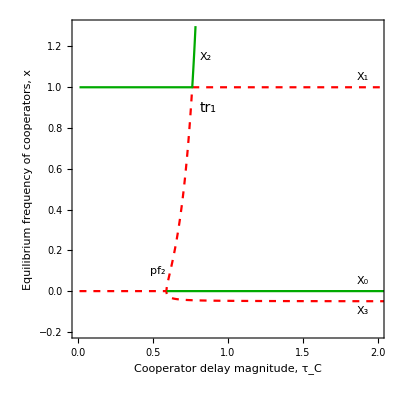

```mathematica
brEig=br[[;;,5]];


brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];

brEig=br[[;;,5]];
brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];
brEqS = ListLinePlot[Transpose[{brtauS ,brXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];
brEqR = ListLinePlot[Transpose[{brtauR ,brXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];

br1Eig=br1[[;;,5]];

br1IdS = Flatten[Position[br1Eig,_?(#<0&)]];
br1IdR = Flatten[Position[br1Eig,_?(#>0&)]];

br1tauS = br1[[br1IdS ,1]];
br1XS = br1[[br1IdS ,2]];
br1tauR = br1[[br1IdR ,1]];
br1XR = br1[[br1IdR ,2]];
br1EqRmid = ListLinePlot[Transpose[{br1tauR,br1XR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];
br1EqUp = ListLinePlot[Transpose[{br1tauS,br1XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.3}}];


 ListLinePlot[Transpose[{br1[[;;,1]] ,br1[[;;,2]]}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];





br2Eig=br2[[;;,5]];

br2IdS = Flatten[Position[br2Eig,_?(#<0&)]];
br2IdR = Flatten[Position[br2Eig,_?(#>0&)]];

br2tauS = br2[[br2IdS ,1]];
br2XS = br2[[br2IdS ,2]];

br2tauR = br2[[br2IdR ,1]];
br2XR = br2[[br2IdR ,2]];

br2EqS = ListLinePlot[Transpose[{br2tauS,br2XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];
br2EqRmid = ListLinePlot[Transpose[{br2tauR,br2XR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 2.0}, {-0.2, 1.1}}];

pfL = Graphics[{Text[Style[HoldForm[Subscript[pf,2]], Medium,Black], {0.53, 0.1} ]}, Background->White];
tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]],  FontSize->14,Black], {0.87, 0.9} ]}, Background->White];
dL = Graphics[{Text[Style["d)",  FontSize->14,Black], ImageScaled[{.18,.93}] ]}, Background->White];
X0L = Graphics[{Text[Style[HoldForm[Subscript[X,0]], Medium,Black], {1.9, 0.05} ]}, Background->White];
X1L = Graphics[{Text[Style[HoldForm[Subscript[X,1]], Medium,Black], {1.9, 1.05} ]}, Background->White];
X2L = Graphics[{Text[Style[HoldForm[Subscript[X,2]], Medium,Black], {0.85, 1.15} ]}, Background->White];
X3L = Graphics[{Text[Style[HoldForm[Subscript[X,3]], Medium,Black], {1.9, -0.1} ]}, Background->White];
fullPlotPitchLower =Show[{brEqS ,brEqR,br1EqRmid,br1EqUp,br2EqS  ,br2EqRmid ,pfL,tr1L ,dL,X0L,X1L,X2L,X3L},PlotRange->{{0.0, 2.0}, {-0.2, 1.3}},Frame->True,
FrameLabel->{"Cooperator delay magnitude, τ_C", "Equilibrium frequency\n of cooperators, x"},
Axes->False,LabelStyle->Directive[Black,14],AspectRatio->1,
PlotRangePadding->None]
```

```mathematica
sn = Import["Snow_2_pris_p_tauC_fold_cont_f.csv"];
tr1= Import["Snow_2_pris_p_tauC_fold_cont_tr.csv"];
tr2 = Import["Snow_2_pris_p_tauC_fold_cont_tr2.csv"];
```

```mathematica
snPlt = ListLinePlot[Transpose[{sn[[;;,1]] ,sn[[;;,2]]}],
PlotStyle->Lighter[Orange,0.4]];
tr1PLt=ListLinePlot[Transpose[{tr1[[;;,1]] ,tr1[[;;,2]]}],PlotStyle->Lighter[Blue,0.4]];
tr2PLt=ListLinePlot[Transpose[{tr2[[;;,1]] ,tr2[[;;,2]]}],PlotStyle->Lighter[Orange,0.4],PlotRange->{{0.55,0.8}, {0.8, 1.4}}];
ScanPltPitch1 =Plot[0.92,{x,0,1},PlotStyle->{Black,Dashed}];
ScanPltPitch2 =Plot[1.192069,{x,0,1},PlotStyle->{Black,Dashed}];
ScanPltTr =Plot[1.15,{x,0,1},PlotStyle->{Black,Dashed}];
tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]],  FontSize->14,Black], {0.78, 0.63} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]],  FontSize->14,Black], {0.42, 1.25} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]],  FontSize->14,Black], {0.42, 1.25} ]}, Background->White];
snL = Graphics[{Text[Style["sn",  FontSize->14,Black], {0.72, 0.63} ]}, Background->White];
bL = Graphics[{Text[Style["b)",  FontSize->14,Black], {0.85, 0.87} ]}, Background->White];
cL = Graphics[{Text[Style["c)",  FontSize->14,Black], {0.85, 1.1} ]}, Background->White];
dL = Graphics[{Text[Style["d)",  FontSize->14,Black], {0.85, 1.22} ]}, Background->White];
aL = Graphics[{Text[Style["a)",  FontSize->14,Black], ImageScaled[{-.18,.93}] ]}, Background->White];
pfL1 = Graphics[{Text[Style[HoldForm[Subscript[pf,1]], Medium,Black], {0.78, 0.95}  ]}, Background->White];
pfL2 = Graphics[{Text[Style[HoldForm[Subscript[pf,2]], Medium,Black], {0.6,1.23} ]}, Background->White];
twoParBif = Show[{snPlt ,tr1PLt,tr2PLt,ScanPltPitch1,ScanPltPitch2,ScanPltTr,tr1L,tr2L ,snL,bL,cL,aL,dL,pfL1 ,pfL2},PlotRange->{{0.4,0.9}, {0.6, 1.4}},Frame->True, LabelStyle->{Medium, Black},
FrameLabel->{"Cooperator delay magnitude, τ_C", "Value of P"},ImageSize->Medium,
AspectRatio->1,
PlotRangePadding->None]
```

-Graphics-

```mathematica
gridPic = GraphicsGrid[{{twoParBif,fullPlotPitch },{fullPlotTranscrit  ,fullPlotPitchLower }},ImageSize->{900,900},Spacings->{10,0}]
SetDirectory[NotebookDirectory[]]
Export["pitchfork_subplots.pdf",gridPic,"PDF","AllowRasterization"->False]
```

-Graphics-

/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv

pitchfork_subplots.pdf